```mathematica
Fibonacci[Range[0,10]]
```

{0,1,1,2,3,5,8,13,21,34,55}

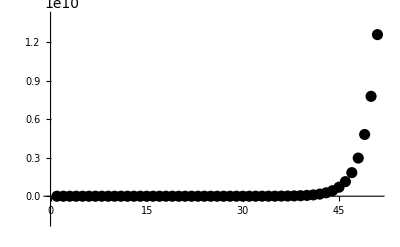

```mathematica
ListPlot[Fibonacci[Range[0,50]],PlotStyle->{PointSize[0.02],Black},PlotRange->{-2 10^9,1.4 10^10}]
```

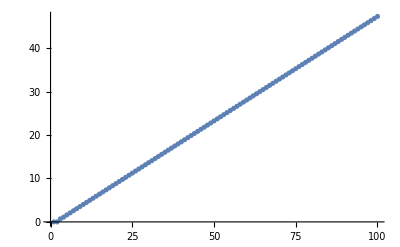

```mathematica
ListPlot[Table[{n,Log[Fibonacci[n]]},{n,1,100}]]
```

```mathematica
linearApprox=Fit[Table[{n,Log[Fibonacci[n]]},{n,50,100}],{1,n},n]
```

-0.804719+0.481212 n

```mathematica
approx=Simplify[ⅇ^linearApprox]
```

0.447214 ⅇ^(0.481212 n)

```mathematica
expApprox=approx/.ⅇ^(a_ n):>(ⅇ^a)^n
```

0.447214 1.61803^n

```mathematica
expApprox/.n->10000
```

3.3644764876487×10^2089

```mathematica
N[Fibonacci[10000]]
```

3.36447648764318×10^2089

```mathematica
expCoeffs=ⅇ^CoefficientList[linearApprox,n]
```

{0.447214,1.61803}

```mathematica
RootApproximant[expCoeffs]
```

{1/(√5),1/2 (1+√5)}

```mathematica
FunctionExpand[Fibonacci[n]]
```

((1/2 (1+√5))^n-(2/(1+√5))^n Cos[n π])/(√5)

```mathematica
Simplify[%19,n∈Integers]
```

-((-2/(1+√5))^n-(1/2 (1+√5))^n)/(√5)

```mathematica
RSolve[{F[n]==F[n-1]+a F[n-2],F[0]==0,F[1]==1},F[n],n]
```

{{F[n]→-(2^-n ((1-√(1+4 a))^n-(1+√(1+4 a))^n))/(√(1+4 a))}}

```mathematica
%24/.a->2
```

{{F[n]→-1/3 2^-n ((-2)^n-4^n)}}

```mathematica
IntegerDigits[25!]
```

{1,5,5,1,1,2,1,0,0,4,3,3,3,0,9,8,5,9,8,4,0,0,0,0,0,0}

```mathematica
DeleteCases[%,0]
```

{1,5,5,1,1,2,1,4,3,3,3,9,8,5,9,8,4}

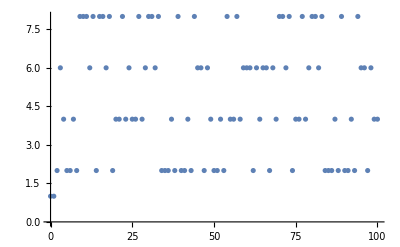

```mathematica
Clear[f];
f[n_]:=Last[DeleteCases[IntegerDigits[n!],0]]
data=Table[{n,f[n]},{n,0,100}];
ListPlot[data]
```

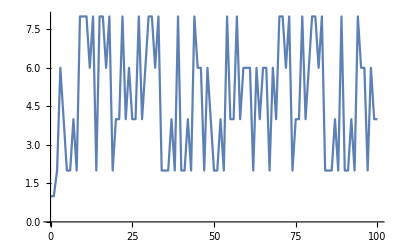

```mathematica
ListLinePlot[data]
```

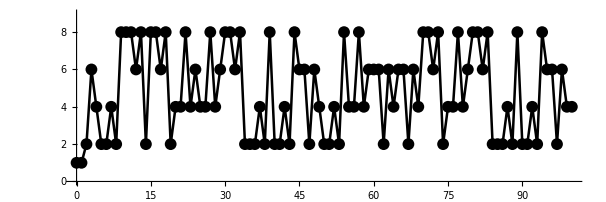

```mathematica
ListLinePlot[data,Mesh->All,MeshStyle->PointSize[0.014],PlotRange->{0,9},AspectRatio->1/3,PlotStyle->{Black,Thickness[0.003]}]
```

```mathematica
freqs=Sort[Tally[Table[f[n],{n,0,1000}]]]
```

{{1,2},{2,249},{4,247},{6,260},{8,243}}

```mathematica
Attributes[Placed]
```

{Protected,ReadProtected}

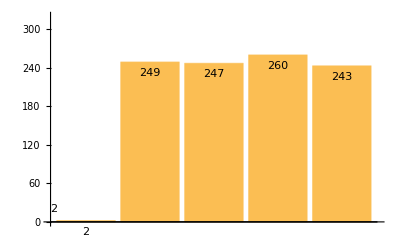

```mathematica
BarChart[Last/@freqs,ChartLabels->Placed[Last/@freqs,Top],PlotRange->{0,320},Epilog->Text[2,{0.5,20}]]
```